# Project

```mathematica
SetDirectory["C:\EDOARDO_01\Università---------------------------\CORSI\VIBRATION\PROGETTO\RELAZIONE\IMMAGINI"]
```

C:\EDOARDO_01\Università---------------------------\CORSI\VIBRATION\PROGETTO\RELAZIONE\IMMAGINI

```mathematica
data ={L->0.7, EE->206*10^9,RHO->7850, A->111*10^-6,JY ->6370*10^-12,dmp1->0.05,dmp2->0.01,dmp3->0.01,C->(EE*JY/(RHO*A))^(1/2)}
```

{L→0.7,EE→206000000000,RHO→7850,A→111/1000000,JY→637/100000000000,dmp1→0.05,dmp2→0.01,dmp3→0.01,C→√((EE JY)/(A RHO))}

## Analytical model

Equation of motion

```mathematica
wxt= W1[x]*T1[t] +W2[x]*T2[t] + W3[x]*T3[t];
```

```mathematica
EQM = C^2*D[wxt,{x,4}]+ D[wxt,{t,2}] ==f
```

W1[x] T1''[t]+W2[x] T2''[t]+W3[x] T3''[t]+C^2 (T1[t] W1^(4)[x]+T2[t] W2^(4)[x]+T3[t] W3^(4)[x])==f

Solution of the space dependent part

```mathematica
W=C1 Cos[β*x]+C2 Sin[β*x]+C3 Cosh[β*x]+C4 Sinh[β*x]
```

C1 Cos[x β]+C3 Cosh[x β]+C2 Sin[x β]+C4 Sinh[x β]

Boundary conditions

```mathematica
B1 = W/. x->0
```

C1+C3

```mathematica
B2 = W/. x->L
```

C1 Cos[L β]+C3 Cosh[L β]+C2 Sin[L β]+C4 Sinh[L β]

```mathematica
B3 = D[W, x,x]/. x->0
```

-C1 β^2+C3 β^2

```mathematica
B4 = D[W, x,x]/. x->L
```

-C1 β^2 Cos[L β]+C3 β^2 Cosh[L β]-C2 β^2 Sin[L β]+C4 β^2 Sinh[L β]

Solution of boundary conditions

```mathematica
C1C3 = Solve[{B1, B3} == 0,{C1,C3}][[1]]
```

{C1→0,C3→0}

```mathematica
B2 = B2/. C1C3
```

C2 Sin[L β]+C4 Sinh[L β]

```mathematica
B4 =  B4/. C1C3
```

-C2 β^2 Sin[L β]+C4 β^2 Sinh[L β]

```mathematica
Det[Normal[CoefficientArrays[{B2,B4},{C2,C4}]][[2]]]
```

2 β^2 Sin[L β] Sinh[L β]

Since Sinh is zero only in the origin, I can remove it:

```mathematica
SolB = Solve[Sin [L*β]==0, β]/.C[1]->k
```

{{β→ConditionalExpression[(2 k π)/L, k∈ℤ]},{β→ConditionalExpression[(π+2 k π)/L, k∈ℤ]}}

## Natural frequencies and mode shapes

```mathematica
βs=Table[(k π)/L,{k,1,3,1}]//.data
```

{4.48799,8.97598,13.464}

```mathematica
ωs = Table[(βs[[k]]^4*C^2)^(1/2),{k,1,3,1}]//.data
```

{781.647,3126.59,7034.82}

```mathematica
freqs=1/(2*π)*ωs
```

{124.403,497.612,1119.63}

### Plots of modes

```mathematica
(*Table [Plot[WS/.β->βs[[i]]/.data,{x,0,2*π},ImageSize->300],{i,1,3,1}]*)
```

```mathematica
scaleplot = 300;
```

Mode 1

```mathematica
W1= W/.C1C3/.C4->0/.C2->1/.β->βs[[1]]
```

Sin[4.48799 x]

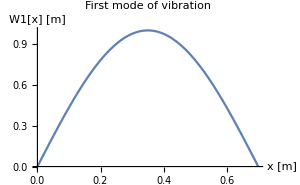

```mathematica
W1plot = Plot[{W1},{x,0,L//.data},ImageSize->scaleplot,PlotLabel->Style["First mode of vibration",20],AxesLabel->{" x [m]","W1[x] [m]"}]
```

```mathematica
Export["PLOT_W1.png",W1plot]
```

PLOT_W1.png

Mode 2

```mathematica
W2= W/.C1C3/.C4->0/.C2->1/.β->βs[[2]]
```

Sin[8.97598 x]

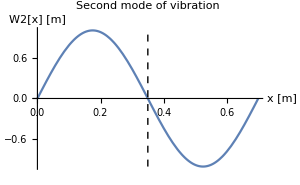

```mathematica
W2plot = Plot[{W2},{x,0,L//.data},ImageSize->scaleplot,PlotLabel->Style["Second mode of vibration",20],AxesLabel->{" x [m]","W2[x] [m]"},Epilog->{Dashed,Line[{{L/2//.data,-1},{L/2//.data,1}}]}]
```

```mathematica
Export["PLOT_W2.png",W2plot]
```

PLOT_W2.png

Mode 3

```mathematica
W3= W/.C1C3/.C4->0/.C2->1/.β->βs[[3]]
```

Sin[13.464 x]

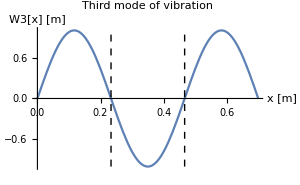

```mathematica
W3plot=Plot[{W3},{x,0,L//.data},ImageSize->scaleplot,PlotLabel->Style["Third mode of vibration",20],AxesLabel->{" x [m]","W3[x] [m]"},Epilog->{Dashed,Line[{{L/3//.data,-1},{L/3//.data,1}}],Line[{{2L/3//.data,-1},{2L/3//.data,1}}]}]
```

```mathematica
Export["PLOT_W3.png",W3plot]
```

PLOT_W3.png

First three modes together

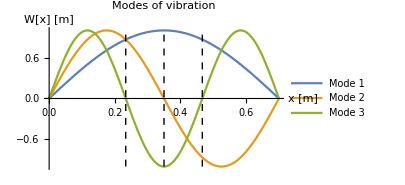

```mathematica
WTOTplot = Plot[{W1,W2,W3},{x,0,L//.data},ImageSize->scaleplot,PlotLegends->{"Mode 1","Mode 2","Mode 3"},PlotLabel->Style["Modes of vibration",20],AxesLabel->{ "x [m]","W[x] [m]"},Epilog->{Dashed,Line[{{L/3//.data,-1},{L/3//.data,1}}],Line[{{2L/3//.data,-1},{2L/3//.data,1}}],Line[{{L/2//.data,-1},{L/2//.data,1}}]}]
```

```mathematica
Export["PLOT_WTOT.png",WTOTplot]
```

PLOT_WTOT.png

## Transfer function

Modal projection of the impulse force f(t, x) ==> modal force

```mathematica
Qn = h[t]*W/.x->L/8/.C1C3/.C4->0/.C2->1
```

h[t] Sin[(L β)/8]

Modal mass

```mathematica
Bn = ∫_0^L W^2 ⅆx/.C1C3/.C4->0/.C2->1/.β->βs[[2]]//.data
```

0.35

Modal oscillator

```mathematica
EQMmod = D[q[t], t,t] +2*ζn*ωn*D[q[t], t]+ ωn^2*q[t]==Qn/(RHO *A*Bn)
```

ωn^2 q[t]+2 ζn ωn q'[t]+q''[t]==(2.85714 h[t] Sin[(L β)/8])/(A RHO)

Modal oscillator in Laplace domain

```mathematica
EQMmodL=LaplaceTransform[ EQMmod,t,s]/.LaplaceTransform[q[t],t,s]->Q[s]/.q[0]->0/.q'[0]->0/.LaplaceTransform[h[t],t,s]->H[s]
```

s^2 Q[s]+2 s ζn ωn Q[s]+ωn^2 Q[s]==(2.85714 H[s] Sin[(L β)/8])/(A RHO)

```mathematica
Qs =Solve[EQMmodL,Q[s]][[1]]
```

{Q[s]→(2.85714 H[s] Sin[0.125 L β])/(A RHO (s^2+2. s ζn ωn+ωn^2))}

Time dependent part of w(x,t)

```mathematica
Ts= Q[s]/.Qs
```

(2.85714 H[s] Sin[0.125 L β])/(A RHO (s^2+2. s ζn ωn+ωn^2))

```mathematica
T1s = Ts/.β->βs[[1]]/.ωn->ωs[[1]]/.ζn->dmp1//.data
```

(1.25481 H[s])/(610972.+78.1647 s+s^2)

```mathematica
T2s = Ts/.β->βs[[2]]/.ωn->ωs[[2]]/.ζn->dmp2//.data
```

(2.31859 H[s])/(9.77555×10^6+62.5318 s+s^2)

```mathematica
T3s = Ts/.β->βs[[3]]/.ωn->ωs[[3]]/.ζn->dmp3//.data
```

(3.02939 H[s])/(4.94887×10^7+140.696 s+s^2)

Transfer function between force and position w(x,t)

```mathematica
wxt= W1*T1 +W2*T2 + W3*T3;
```

```mathematica
wxtS= wxt/.T1->T1s/.T2->T2s/.T3->T3s/.x->L/2//.data
```

(2.83946×10^-16 H[s])/(9.77555×10^6+62.5318 s+s^2)+(1.25481 H[s])/(610972.+78.1647 s+s^2)-(3.02939 H[s])/(4.94887×10^7+140.696 s+s^2)

Transfer function between force and acceleration ∂_(t,t) w(x,t)

```mathematica
TF = Simplify@(wxtS/(H [s]))*(s^2)
```

s^2 ((2.83946×10^-16)/(9.77555×10^6+62.5318 s+s^2)+1.25481/(610972.+78.1647 s+s^2)-3.02939/(4.94887×10^7+140.696 s+s^2))

```mathematica
MODTF = FullSimplify[Abs[TF]/.s->ω*I]
```

Abs[ω^2 (-(2.83946×10^-16)/(-9.77555×10^6+ω ((0.-62.5318 ⅈ)+ω))-1.25481/(-610972.+ω ((0.-78.1647 ⅈ)+ω))+3.02939/(-4.94887×10^7+ω ((0.-140.696 ⅈ)+ω)))]

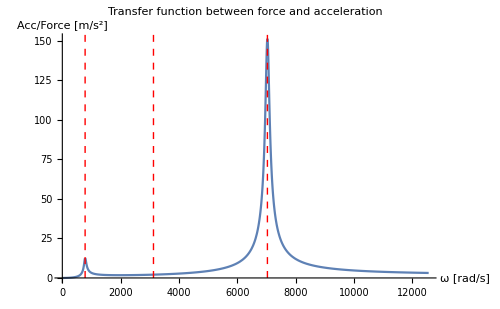

```mathematica
TFplot  = Plot[MODTF,{ω,0,2*π*2000},PlotRange->Full,PlotLabel->Style["Transfer function between force and acceleration",20],AxesLabel->{" ω [rad/s]", "Acc/Force [m/s^2]"},ImageSize->500,Epilog->{Dashed,Red,Line[{{ωs[[1]],0},{ωs[[1]],200}}],Line[{{ωs[[2]],0},{ωs[[2]],200}}],Line[{{ωs[[3]],0},{ωs[[3]],200}}],Text[IntegerPart[ωs[[1]]],{ωs[[1]],-5.3}],Text[IntegerPart[ωs[[2]]],{ωs[[2]],-5.3}],Text[IntegerPart[ωs[[3]]],{ωs[[3]],-5.3}]}]
```

```mathematica
Export["PLOT_TF.png",TFplot]
```

PLOT_TF.png

Create a vector of values to compare the real and the ideal transfer function in Matlab

```mathematica
vecMODTF =Table [MODTF/.ω->2*π*f,{f,0,2000,1}];
```

```mathematica
SetDirectory["C:\EDOARDO_01\Università---------------------------\CORSI\VIBRATION\PROGETTO"]
```

C:\EDOARDO_01\Università---------------------------\CORSI\VIBRATION\PROGETTO

```mathematica
Export["dataTF.txt",vecMODTF]
```

dataTF.txt

## RAYLEIGH’S METHOD TO FIND THE NATURAL FREQUENCIES

```mathematica
Wv = {W1,W2,W3};
```

```mathematica
ωR= Table[((∫_0^L EE*JY*(D[Wv[[i]], x,x])^2 ⅆx)/(∫_0^L RHO*A*Wv[[i]]^2 ⅆx))^0.5,{i,1,3,1}]//.data
```

{781.647,3126.59,7034.82}